# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - Right Handed Helicity Fraction - SM )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

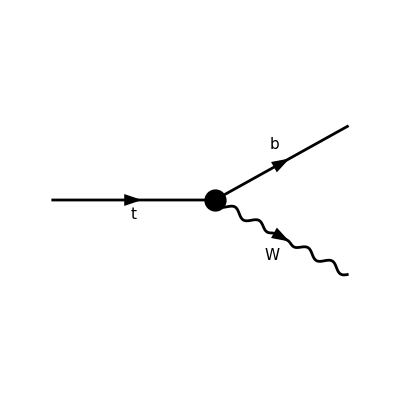

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

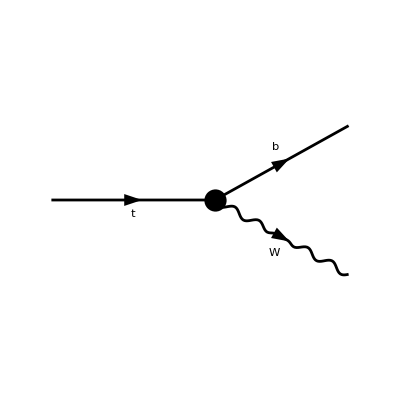

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc139L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc139R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc139L =(FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
     gc139R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
Eprh=1/(Sqrt[2]){0,-Cos[θ]Cos[ϕ]-I Sin[ϕ],-Cos[θ] Sin[ϕ]+I Cos[ϕ],Sin[θ]};
Epcrh=1/(Sqrt[2]){0,-Cos[θ]Cos[ϕ]+I Sin[ϕ],-Cos[θ] Sin[ϕ]-I Cos[ϕ],Sin[θ]};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
LeviCivita[indices__]:=-Module[{list={indices}},If[Length[list]≠4||DuplicateFreeQ[list]===False,0,Signature[list]]]
LeviCivitaContraction[Pb_,pt_,Epclh_,Eplh_]:=Sum[LeviCivita[mu,nu,rho,sigma]*Pb[[mu+1]] pt[[nu+1]] Epclh[[rho+1]]*Eplh[[sigma+1]],{mu,0,3},{nu,0,3},{rho,0,3},{sigma,0,3}]//Simplify
```

```mathematica
Msqtr=(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[Pb,Pt,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[Pt,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[Pt,Eprh]-MinkSP[Pb,Pt]*MinkSP[Epcrh,Eprh])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[Pb,Pt,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[Pt,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[Pt,Eprh]-MinkSP[Pb,Pt]*MinkSP[Epcrh,Eprh])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[Pb,Pw,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[Pw,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[Pw,Eprh]-2 MinkSP[Pb,Pw]*MinkSP[Epcrh,Eprh])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epcrh,Eprh]+I (MinkSP[Pt,Eprh]*MinkSP[Pw,Epcrh]+MinkSP[Pt,Epcrh]*MinkSP[Pw,Eprh]))+MinkSP[Epcrh,Eprh]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[Pt,Pw]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epcrh,Eprh]+I (MinkSP[Pt,Eprh]*MinkSP[Pw,Epcrh]+MinkSP[Pt,Epcrh]*MinkSP[Pw,Eprh]))+MinkSP[Epcrh,Eprh]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epcrh]*MinkSP[Pw,Eprh]-MinkSP[Pw,Pw]*MinkSP[Epcrh,Eprh])-4 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epcrh,Eprh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[Pt,Epcrh]*MinkSP[Pw,Eprh]-2 MinkSP[Pt,Pw]*MinkSP[Epcrh,Eprh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g MinkSP[Pt,Eprh] MinkSP[Pw,Epcrh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epcrh]*MinkSP[Pw,Eprh]-MinkSP[Pw,Pw]*MinkSP[Epcrh,Eprh])-2 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epcrh,Eprh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[Pt,Eprh]*MinkSP[Pw,Epcrh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[Pt,Epcrh]*MinkSP[Pw,Eprh]-2 MinkSP[Pt,Pw]*MinkSP[Epcrh,Eprh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[Pb,Pt,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[Pt,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[Pt,Eprh]-MinkSP[Pb,Pt]*MinkSP[Epcrh,Eprh])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[Pb,Pw,Epcrh,Eprh]+MinkSP[Pb,Eprh]*MinkSP[Pw,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[Pw,Eprh]-2 MinkSP[Pb,Pw]*MinkSP[Epcrh,Eprh])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[Pb,Pw,Epcrh,Eprh]*MinkSP[Pt,Pw]+MinkSP[Pb,Eprh]*MinkSP[Pw,Epcrh]*MinkSP[Pt,Pw]+MinkSP[Pb,Epcrh]*MinkSP[Pw,Eprh]*MinkSP[Pt,Pw]+MinkSP[Pb,Pw]*MinkSP[Pt,Eprh]*MinkSP[Pw,Epcrh]+MinkSP[Pb,Pw]*MinkSP[Pt,Epcrh]*MinkSP[Pw,Eprh]-MinkSP[Pb,Pt]*MinkSP[Pw,Epcrh]*MinkSP[Pw,Eprh]-I ((LeviCivitaContraction[Pb,Pt,Epcrh,Eprh]-I (MinkSP[Pb,Eprh]*MinkSP[Pt,Epcrh]+MinkSP[Pb,Epcrh]*MinkSP[Pt,Eprh]))*MinkSP[Pw,Pw]-LeviCivitaContraction[Pb,Pt,Pw,Eprh]*MinkSP[Pw,Epcrh]+LeviCivitaContraction[Pb,Pt,Pw,Epcrh]*MinkSP[Pw,Eprh])+(MinkSP[Pb,Pt]*MinkSP[Pw,Pw]-2 MinkSP[Pb,Pw]*MinkSP[Pt,Pw])*MinkSP[Epcrh,Eprh]))+Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Eprh] MinkSP[Pw,Epcrh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Eprh] MinkSP[Pw,Epcrh] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Epcrh] MinkSP[Pw,Eprh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Epcrh] MinkSP[Pw,Eprh] Lambda^4-128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Epcrh] MinkSP[Pw,Eprh] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh] Lambda^4-256 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epcrh,Eprh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epcrh,Eprh] Lambda^4-32 g^2 vev^4 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Eprh] MinkSP[Pw,Epcrh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Eprh] MinkSP[Pw,Epcrh] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Epcrh] MinkSP[Pw,Eprh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Epcrh] MinkSP[Pw,Eprh] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Epcrh] MinkSP[Pw,Eprh] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epcrh,Eprh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epcrh,Eprh] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh] Re[C2q2H4D] Lambda^2+32 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Eprh] MinkSP[Pw,Epcrh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Eprh] MinkSP[Pw,Epcrh]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Epcrh] MinkSP[Pw,Eprh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Epcrh] MinkSP[Pw,Eprh]-32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Epcrh] MinkSP[Pw,Eprh]+4 C2q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh]-3 C3q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh]-64 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epcrh,Eprh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epcrh,Eprh]-16 C2q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[Pb,Pw] MinkSP[Epcrh,Eprh] Re[C2q2H4D]-I LeviCivitaContraction[Pb,Pt,Epcrh,Eprh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[Pb,Pw,Epcrh,Eprh]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+4 C3q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epcrh,Eprh] Re[C3q2H4D]+MinkSP[Pb,Eprh]*(MinkSP[Pt,Epcrh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Epcrh]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+MinkSP[Pb,Epcrh]*(MinkSP[Pt,Eprh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Eprh]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))//FullSimplify
```

1/(32 Lambda^8)mt Nc (32 (Eb+pb) (EW+pb)^2 vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 (Eb+pb) (EW+pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 (Eb+pb) vev^4 Conjugate[CHud]^2+4 g^2 (Eb+pb) vev^8 Conjugate[CudH4D]^2+32 Lambda^2 (EW+pb) vev Conjugate[CbW] (4 mb (-EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (Eb+pb) vev^2 Conjugate[CHud]+(Eb+pb) vev^4 Conjugate[CudH4D]-mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 (EW+pb) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 (Eb+pb) (EW+pb) vev Conjugate[CbW]+4 mb (-EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (Eb+pb) vev^2 Conjugate[CHud]+(Eb+pb) vev^4 Conjugate[CudH4D]-mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g Lambda^2 vev^2 Conjugate[CHud] (-g (Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 g Lambda^4+(C2q2H4D+C3q2H4D) g vev^4+2 √2 (EW-pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4+(C2q2H4D+C3q2H4D) g vev^4+2 √2 (EW-pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 (Eb-pb)+64 √2 CtW g Lambda^6 (-Eb+pb) (-EW+pb) vev+128 CtW^2 Lambda^4 (Eb-pb) (EW-pb)^2 vev^2+32 √2 C1quWH3 g Lambda^4 (-Eb+pb) (-EW+pb) vev^3+128 C1quWH3 CtW Lambda^2 (Eb-pb) (EW-pb)^2 vev^4+32 √2 C3q2H4D CtW g Lambda^2 (-Eb+pb) (-EW+pb) vev^5+32 C1quWH3^2 (Eb-pb) (EW-pb)^2 vev^6+g^2 (C3q2H4D^2 (Eb-3 pb)+4 C2q2H4D^2 (Eb+pb)) vev^8+g vev^2 (8 C2q2H4D Eb g vev^6 Conjugate[C2q2H4D]+4 g (Eb-pb) vev^6 Conjugate[C2q2H4D]^2+16 g Lambda^4 (Eb-pb) vev^2 Conjugate[C3phiq]^2-2 C3q2H4D Eb g vev^6 Conjugate[C3q2H4D]+g (Eb-pb) vev^6 Conjugate[C3q2H4D]^2+8 Lambda^2 (Eb-pb) Conjugate[C3phiq] (4 g Lambda^4+4 √2 (EW-pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+4 vev^2 (8 √2 CtW Lambda^2 (Eb-pb) (EW-pb) vev (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+4 g Lambda^4 (Eb-pb) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+4 √2 C1quWH3 (Eb-pb) (EW-pb) vev^3 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g vev^4 (-4 (C2q2H4D pb+ⅈ (-Eb+pb) Im[C3q2H4D]) Re[C2q2H4D]+C3q2H4D pb Re[C3q2H4D])))))

```mathematica
Msqtot=(1/(32 Lambda^8 MinkSP[Pw,Pw])) Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^4-8 g Lambda^2 Conjugate[CHud] (3 MinkSP[Pw,Pw] (mb Conjugate[CKM3x3] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 Sqrt[2] mt vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) MinkSP[Pb,Pw])-g vev^4 Conjugate[CudH4D] (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw])) vev^2-24 mb Conjugate[CKM3x3] MinkSP[Pw,Pw] (g Conjugate[CudH4D] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw]+Sqrt[2] g MinkSP[Pt,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))) vev+4 (g^2 (Conjugate[CudH4D])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^8+12 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] MinkSP[Pb,Pw] MinkSP[Pw,Pw] vev^5-8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 MinkSP[Pw,Pw] (MinkSP[Pb,Pt] MinkSP[Pw,Pw]-4 MinkSP[Pb,Pw] MinkSP[Pt,Pw]))+(Conjugate[CKM3x3])^2 (MinkSP[Pb,Pt] MinkSP[Pw,Pw] (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+2 MinkSP[Pb,Pw] (MinkSP[Pt,Pw] (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 I Im[C3q2H4D] Re[C2q2H4D])) g^2+24 Sqrt[2] mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) g+64 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2 MinkSP[Pt,Pw] MinkSP[Pw,Pw])))//FullSimplify
```

1/(32 Lambda^8 (EW-pb) (EW+pb))Nc (4 g^2 Lambda^4 mt (3 Eb EW^2-(Eb-2 EW) pb^2) vev^4 Conjugate[CHud]^2+4 mt (8 (EW-pb) (EW+pb) (3 Eb EW^2+(Eb+4 EW) pb^2) (vev^3 Conjugate[C1qdWH3]+2 Lambda^2 vev Conjugate[CbW])^2+12 √2 g (EW-pb) (EW+pb) (Eb EW+pb^2) vev^5 (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) Conjugate[CudH4D]+g^2 (3 Eb EW^2-(Eb-2 EW) pb^2) vev^8 Conjugate[CudH4D]^2)-8 g Lambda^2 vev^2 Conjugate[CHud] (g mt (-2 EW pb^2+Eb (-3 EW^2+pb^2)) vev^4 Conjugate[CudH4D]+3 (EW-pb) (EW+pb) (-2 √2 mt (Eb EW+pb^2) vev (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])+mb mt Conjugate[CKM3x3] (2 √2 EW vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))-24 mb (EW-pb) (EW+pb) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (2 √2 EW vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (4 mt (EW-pb) (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 EW g mt (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (2 mt (Eb EW+pb^2) (64 EW (EW-pb) (EW+pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2+24 √2 g (EW-pb) (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+EW g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+Eb mt (EW-pb) (EW+pb) (-32 (EW-pb) (EW+pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2+g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)+g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
EW=(mt^2+mw^2-mb^2)/(2 mt);
```

```mathematica
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthRight=Integrate[Msqtr *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

1/(1024 Lambda^8 mt^5 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (8 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^6 Conjugate[C1qdWH3]^2+32 Lambda^4 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2-16 Lambda^2 mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mt^2 (mb^2-mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CbW]-4 mb mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g mt (Lambda^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 g Lambda^2 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (2 g Lambda^4 mt+(C2q2H4D+C3q2H4D) g mt vev^4-√2 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4 mt+(C2q2H4D+C3q2H4D) g mt vev^4-√2 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+mt^2 Conjugate[CKM3x3]^2 (32 (mb^4+mt^2 (mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+mb^2 (-2 mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))) (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2-16 √2 g mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g^2 (-16 Lambda^8 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))-16 (C2q2H4D+C3q2H4D) Lambda^4 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^4+(C3q2H4D^2 (mb^2+mt^2-mw^2-3 √(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+4 C2q2H4D^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))) vev^8)+g vev^2 (-8 vev^2 (2 g Lambda^4 √(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))+2 √2 mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)-g (mb^2+mt^2-mw^2) (2 Lambda^4+C2q2H4D vev^4)) Conjugate[C2q2H4D]+4 g (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^6 Conjugate[C2q2H4D]^2-16 g Lambda^4 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^2 Conjugate[C3phiq]^2-2 C3q2H4D g (mb^2+mt^2-mw^2) vev^6 Conjugate[C3q2H4D]+g (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^6 Conjugate[C3q2H4D]^2-16 g vev^6 (C2q2H4D √(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))+ⅈ (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) Im[C3q2H4D]) Re[C2q2H4D]-8 Lambda^2 Conjugate[C3phiq] (4 g Lambda^4 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+4 √2 mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+4 vev^2 (4 g Lambda^4 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+C3q2H4D g √(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))) vev^4+4 √2 mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)) Re[C3q2H4D])))

```mathematica
DecayWidthRightSM=DecayWidthRight/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

-(g^2 √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) Nc Conjugate[CKM3x3]^2)/(64 mt^3 π)

```mathematica
(*Total Decay Width*)
```

```mathematica
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthtotal=Integrate[Msqtot*dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
(* SM limit *)
```

```mathematica
DecayWidthTotalSM=DecayWidthtotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √(-((mb-mt-mw) (mb+mt-mw))) ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
FR=DecayWidthRight/DecayWidthtotal//FullSimplify
```

(4 mt^2 mw^2 (8 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^6 Conjugate[C1qdWH3]^2+32 Lambda^4 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2-16 Lambda^2 mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mt^2 (mb^2-mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CbW]-4 mb mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g mt (Lambda^2 (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 g Lambda^2 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (2 g Lambda^4 mt+(C2q2H4D+C3q2H4D) g mt vev^4-√2 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4 mt+(C2q2H4D+C3q2H4D) g mt vev^4-√2 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+mt^2 Conjugate[CKM3x3]^2 (32 (mb^4+mt^2 (mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+mb^2 (-2 mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))) (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2-16 √2 g mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g^2 (-16 Lambda^8 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))-16 (C2q2H4D+C3q2H4D) Lambda^4 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^4+(C3q2H4D^2 (mb^2+mt^2-mw^2-3 √(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+4 C2q2H4D^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))) vev^8)+g vev^2 (-8 vev^2 (2 g Lambda^4 √(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))+2 √2 mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)-g (mb^2+mt^2-mw^2) (2 Lambda^4+C2q2H4D vev^4)) Conjugate[C2q2H4D]+4 g (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^6 Conjugate[C2q2H4D]^2-16 g Lambda^4 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^2 Conjugate[C3phiq]^2-2 C3q2H4D g (mb^2+mt^2-mw^2) vev^6 Conjugate[C3q2H4D]+g (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^6 Conjugate[C3q2H4D]^2-16 g vev^6 (C2q2H4D √(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))+ⅈ (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) Im[C3q2H4D]) Re[C2q2H4D]-8 Lambda^2 Conjugate[C3phiq] (4 g Lambda^4 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+4 √2 mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+4 vev^2 (4 g Lambda^4 (-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+C3q2H4D g √(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))) vev^4+4 √2 mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)) Re[C3q2H4D]))))/(16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) (2 CtW Lambda^2 vev+C1quWH3 vev^3)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
(* SM Limit*)
```

```mathematica
FRSM=FR/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(mw^2 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)))/((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)

```mathematica
FRSM=DecayWidthRightSM/DecayWidthTotalSM//FullSimplify
```

-(mw^2 (-mb^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))-mt^2+mw^2))/(mw^2 (mb^2+mt^2)+(mb^2-mt^2)^2-2 mw^4)